```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Rest[Import["nr-station-links.csv"]];
```

```mathematica
edges=(#[[1]]->#[[2]])&/@data;
weights=data[[All,3]];
g=Graph[edges,EdgeWeight->weights];
```

```mathematica
tmp=FindShortestPath[g,"BHM","EDB"]
```

{BHM,SGB,SAD,DDP,TIP,CSY,WVH,PKG,STA,CRE,WSF,HTF,ACB,WBQ,WGN,EBA,LEY,PRE,LAN,OXN,PNR,CAR,LOC,CRS,KKN,CUH,WTA,KGE,SLA,HYM,EDB}

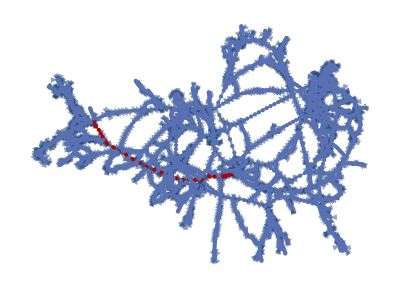

```mathematica
HighlightGraph[g,PathGraph[tmp]]
```

```mathematica
GraphDistance[g,"BHM","EDB"]
```

295.91